good video: https://www.youtube.com/watch?v=g7zFl8EnbzI

```mathematica
bimg=-Graphics-;
fimg=-Graphics-;
mimg=-Graphics-;
```

```mathematica
cfimg=ColorConvert[fimg,"GrayScale"];
cbimg=ColorConvert[bimg,"GrayScale"];
```

```mathematica
PrependTo[$Path,NotebookDirectory[]];
<<poisson.m
<<implementation.m
```

```mathematica
res={};
Do[
fimgData=ImageData[rfimg=ImageResize[cfimg,{n,n}]];
bimgData=ImageData[rbimg=ImageResize[cbimg,{n,n}]];
mimgData=Unitize[ImageData[rmimg=Image[ImageResize[mimg,{n,n}],"Bit"]]];
{A,b}=constructMatricies[rfimg,rbimg,rmimg];
vars=Table[ToExpression["v"<>ToString[i]],{i,1,Last[Dimensions[A]]}];
AppendTo[res,n->Quiet@CompareMethods[Norm[A.vars-b],vars]],
{n,10,200}
]
```

$Aborted

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"result.mx"}],res]
```

```mathematica
res
```

{10→<|VariableCount→68,QuasiNewton→<|EvaluationTime→0.631,EvaluationCount→1788,StepCount→56|>,PolakRibiere→<|EvaluationTime→0.032,EvaluationCount→960,StepCount→21|>|>,11→<|VariableCount→86,QuasiNewton→<|EvaluationTime→0.09,EvaluationCount→2960,StepCount→67|>,PolakRibiere→<|EvaluationTime→0.048,EvaluationCount→1664,StepCount→25|>|>,12→<|VariableCount→106,QuasiNewton→<|EvaluationTime→0.13,EvaluationCount→3888,StepCount→73|>,PolakRibiere→<|EvaluationTime→0.048,EvaluationCount→1440,StepCount→17|>|>,13→<|VariableCount→114,QuasiNewton→<|EvaluationTime→0.132,EvaluationCount→3708,StepCount→73|>,PolakRibiere→<|EvaluationTime→0.051,EvaluationCount→1458,StepCount→23|>|>,14→<|VariableCount→137,QuasiNewton→<|EvaluationTime→0.25,EvaluationCount→5520,StepCount→74|>,PolakRibiere→<|EvaluationTime→0.11,EvaluationCount→2784,StepCount→25|>|>,15→<|VariableCount→162,QuasiNewton→<|EvaluationTime→0.333,EvaluationCount→6831,StepCount→80|>,PolakRibiere→<|EvaluationTime→0.11,EvaluationCount→2376,StepCount→25|>|>,16→<|VariableCount→173,QuasiNewton→<|EvaluationTime→0.458,EvaluationCount→8800,StepCount→83|>,PolakRibiere→<|EvaluationTime→0.166,EvaluationCount→3360,StepCount→25|>|>,17→<|VariableCount→201,QuasiNewton→<|EvaluationTime→0.603,EvaluationCount→9554,StepCount→86|>,PolakRibiere→<|EvaluationTime→0.188,EvaluationCount→3298,StepCount→24|>|>,18→<|VariableCount→230,QuasiNewton→<|EvaluationTime→0.791,EvaluationCount→11590,StepCount→90|>,PolakRibiere→<|EvaluationTime→0.208,EvaluationCount→3192,StepCount→23|>|>,19→<|VariableCount→243,QuasiNewton→<|EvaluationTime→0.826,EvaluationCount→10947,StepCount→76|>,PolakRibiere→<|EvaluationTime→0.432,EvaluationCount→5289,StepCount→25|>|>,20→<|VariableCount→276,QuasiNewton→<|EvaluationTime→1.34,EvaluationCount→14688,StepCount→86|>,PolakRibiere→<|EvaluationTime→0.396,EvaluationCount→4656,StepCount→22|>|>,21→<|VariableCount→311,QuasiNewton→<|EvaluationTime→1.525,EvaluationCount→16524,StepCount→85|>,PolakRibiere→<|EvaluationTime→0.508,EvaluationCount→5940,StepCount→25|>|>,22→<|VariableCount→326,QuasiNewton→<|EvaluationTime→1.772,EvaluationCount→17328,StepCount→84|>,PolakRibiere→<|EvaluationTime→0.397,EvaluationCount→4218,StepCount→20|>|>,23→<|VariableCount→364,QuasiNewton→<|EvaluationTime→2.46,EvaluationCount→22754,StepCount→100|>,PolakRibiere→<|EvaluationTime→0.708,EvaluationCount→7006,StepCount→26|>|>,24→<|VariableCount→403,QuasiNewton→<|EvaluationTime→1.669,EvaluationCount→14756,StepCount→66|>,PolakRibiere→<|EvaluationTime→0.821,EvaluationCount→7684,StepCount→23|>|>,25→<|VariableCount→420,QuasiNewton→<|EvaluationTime→3.147,EvaluationCount→22908,StepCount→90|>,PolakRibiere→<|EvaluationTime→0.743,EvaluationCount→6003,StepCount→23|>|>,26→<|VariableCount→463,QuasiNewton→<|EvaluationTime→2.757,EvaluationCount→18426,StepCount→64|>,PolakRibiere→<|EvaluationTime→0.95,EvaluationCount→7719,StepCount→20|>|>,27→<|VariableCount→507,QuasiNewton→<|EvaluationTime→3.583,EvaluationCount→22659,StepCount→77|>,PolakRibiere→<|EvaluationTime→1.082,EvaluationCount→6806,StepCount→21|>|>,28→<|VariableCount→527,QuasiNewton→<|EvaluationTime→3.908,EvaluationCount→25298,StepCount→80|>,PolakRibiere→<|EvaluationTime→1.055,EvaluationCount→7280,StepCount→21|>|>,29→<|VariableCount→574,QuasiNewton→<|EvaluationTime→3.795,EvaluationCount→23226,StepCount→72|>,PolakRibiere→<|EvaluationTime→1.559,EvaluationCount→10094,StepCount→23|>|>,30→<|VariableCount→624,QuasiNewton→<|EvaluationTime→4.356,EvaluationCount→22671,StepCount→69|>,PolakRibiere→<|EvaluationTime→1.476,EvaluationCount→8613,StepCount→21|>|>,31→<|VariableCount→645,QuasiNewton→<|EvaluationTime→6.439,EvaluationCount→29719,StepCount→77|>,PolakRibiere→<|EvaluationTime→2.177,EvaluationCount→9266,StepCount→21|>|>,32→<|VariableCount→698,QuasiNewton→<|EvaluationTime→7.337,EvaluationCount→32248,StepCount→80|>,PolakRibiere→<|EvaluationTime→2.309,EvaluationCount→10556,StepCount→24|>|>,33→<|VariableCount→752,QuasiNewton→<|EvaluationTime→9.658,EvaluationCount→38308,StepCount→89|>,PolakRibiere→<|EvaluationTime→2.663,EvaluationCount→12078,StepCount→22|>|>,34→<|VariableCount→776,QuasiNewton→<|EvaluationTime→10.958,EvaluationCount→47520,StepCount→94|>,PolakRibiere→<|EvaluationTime→2.326,EvaluationCount→10530,StepCount→21|>|>,35→<|VariableCount→833,QuasiNewton→<|EvaluationTime→10.585,EvaluationCount→43018,StepCount→91|>,PolakRibiere→<|EvaluationTime→3.726,EvaluationCount→15481,StepCount→25|>|>,36→<|VariableCount→857,QuasiNewton→<|EvaluationTime→14.,EvaluationCount→52096,StepCount→98|>,PolakRibiere→<|EvaluationTime→3.399,EvaluationCount→14504,StepCount→24|>|>,37→<|VariableCount→918,QuasiNewton→<|EvaluationTime→11.68,EvaluationCount→41808,StepCount→79|>,PolakRibiere→<|EvaluationTime→3.5,EvaluationCount→13416,StepCount→24|>|>,38→<|VariableCount→981,QuasiNewton→<|EvaluationTime→12.646,EvaluationCount→40750,StepCount→73|>,PolakRibiere→<|EvaluationTime→4.173,EvaluationCount→13529,StepCount→24|>|>,39→<|VariableCount→1007,QuasiNewton→<|EvaluationTime→18.978,EvaluationCount→47502,StepCount→80|>,PolakRibiere→<|EvaluationTime→5.463,EvaluationCount→16008,StepCount→24|>|>,40→<|VariableCount→1072,QuasiNewton→<|EvaluationTime→17.913,EvaluationCount→53382,StepCount→82|>,PolakRibiere→<|EvaluationTime→4.703,EvaluationCount→15996,StepCount→22|>|>,41→<|VariableCount→1140,QuasiNewton→<|EvaluationTime→23.239,EvaluationCount→66816,StepCount→96|>,PolakRibiere→<|EvaluationTime→5.664,EvaluationCount→17088,StepCount→21|>|>,42→<|VariableCount→1168,QuasiNewton→<|EvaluationTime→19.19,EvaluationCount→50148,StepCount→77|>,PolakRibiere→<|EvaluationTime→7.416,EvaluationCount→18308,StepCount→22|>|>,43→<|VariableCount→1239,QuasiNewton→<|EvaluationTime→27.845,EvaluationCount→70406,StepCount→91|>,PolakRibiere→<|EvaluationTime→7.621,EvaluationCount→18618,StepCount→25|>|>,44→<|VariableCount→1311,QuasiNewton→<|EvaluationTime→24.687,EvaluationCount→57405,StepCount→77|>,PolakRibiere→<|EvaluationTime→8.534,EvaluationCount→21285,StepCount→24|>|>,45→<|VariableCount→1341,QuasiNewton→<|EvaluationTime→36.596,EvaluationCount→81774,StepCount→100|>,PolakRibiere→<|EvaluationTime→7.279,EvaluationCount→18249,StepCount→22|>|>,46→<|VariableCount→1417,QuasiNewton→<|EvaluationTime→32.221,EvaluationCount→67962,StepCount→85|>,PolakRibiere→<|EvaluationTime→10.768,EvaluationCount→23859,StepCount→23|>|>,47→<|VariableCount→1495,QuasiNewton→<|EvaluationTime→39.042,EvaluationCount→73041,StepCount→83|>,PolakRibiere→<|EvaluationTime→12.254,EvaluationCount→22339,StepCount→24|>|>,48→<|VariableCount→1527,QuasiNewton→<|EvaluationTime→41.581,EvaluationCount→74046,StepCount→82|>,PolakRibiere→<|EvaluationTime→10.676,EvaluationCount→23220,StepCount→22|>|>,49→<|VariableCount→1608,QuasiNewton→<|EvaluationTime→43.089,EvaluationCount→79696,StepCount→83|>,PolakRibiere→<|EvaluationTime→12.041,EvaluationCount→24208,StepCount→23|>|>,50→<|VariableCount→1690,QuasiNewton→<|EvaluationTime→61.196,EvaluationCount→99876,StepCount→100|>,PolakRibiere→<|EvaluationTime→11.357,EvaluationCount→22673,StepCount→20|>|>,51→<|VariableCount→1724,QuasiNewton→<|EvaluationTime→52.24,EvaluationCount→82052,StepCount→82|>,PolakRibiere→<|EvaluationTime→14.431,EvaluationCount→25988,StepCount→21|>|>,52→<|VariableCount→1810,QuasiNewton→<|EvaluationTime→52.741,EvaluationCount→76076,StepCount→72|>,PolakRibiere→<|EvaluationTime→13.67,EvaluationCount→22792,StepCount→17|>|>,53→<|VariableCount→1897,QuasiNewton→<|EvaluationTime→71.45,EvaluationCount→95256,StepCount→85|>,PolakRibiere→<|EvaluationTime→17.878,EvaluationCount→25920,StepCount→17|>|>,54→<|VariableCount→1934,QuasiNewton→<|EvaluationTime→87.618,EvaluationCount→116181,StepCount→100|>,PolakRibiere→<|EvaluationTime→22.109,EvaluationCount→33431,StepCount→22|>|>,55→<|VariableCount→2024,QuasiNewton→<|EvaluationTime→83.247,EvaluationCount→103454,StepCount→87|>,PolakRibiere→<|EvaluationTime→28.371,EvaluationCount→38060,StepCount→26|>|>,56→<|VariableCount→2117,QuasiNewton→<|EvaluationTime→83.939,EvaluationCount→98767,StepCount→83|>,PolakRibiere→<|EvaluationTime→24.658,EvaluationCount→26175,StepCount→17|>|>,57→<|VariableCount→2155,QuasiNewton→<|EvaluationTime→115.994,EvaluationCount→132487,StepCount→96|>,PolakRibiere→<|EvaluationTime→23.139,EvaluationCount→29360,StepCount→14|>|>,58→<|VariableCount→2251,QuasiNewton→<|EvaluationTime→90.172,EvaluationCount→94736,StepCount→72|>,PolakRibiere→<|EvaluationTime→28.793,EvaluationCount→33234,StepCount→20|>|>,59→<|VariableCount→2290,QuasiNewton→<|EvaluationTime→105.756,EvaluationCount→110544,StepCount→82|>,PolakRibiere→<|EvaluationTime→24.636,EvaluationCount→27048,StepCount→16|>|>,60→<|VariableCount→2389,QuasiNewton→<|EvaluationTime→141.081,EvaluationCount→132088,StepCount→87|>,PolakRibiere→<|EvaluationTime→35.601,EvaluationCount→35530,StepCount→17|>|>,61→<|VariableCount→2489,QuasiNewton→<|EvaluationTime→123.385,EvaluationCount→105570,StepCount→72|>,PolakRibiere→<|EvaluationTime→39.107,EvaluationCount→33948,StepCount→17|>|>,62→<|VariableCount→2530,QuasiNewton→<|EvaluationTime→185.32,EvaluationCount→151548,StepCount→100|>,PolakRibiere→<|EvaluationTime→39.151,EvaluationCount→37230,StepCount→18|>|>,63→<|VariableCount→2634,QuasiNewton→<|EvaluationTime→147.823,EvaluationCount→121408,StepCount→80|>,PolakRibiere→<|EvaluationTime→42.382,EvaluationCount→40768,StepCount→20|>|>,64→<|VariableCount→2740,QuasiNewton→<|EvaluationTime→162.207,EvaluationCount→117180,StepCount→75|>,PolakRibiere→<|EvaluationTime→43.694,EvaluationCount→36270,StepCount→16|>|>,65→<|VariableCount→2783,QuasiNewton→<|EvaluationTime→180.621,EvaluationCount→125280,StepCount→78|>,PolakRibiere→<|EvaluationTime→52.033,EvaluationCount→40800,StepCount→24|>|>,66→<|VariableCount→2891,QuasiNewton→<|EvaluationTime→145.123,EvaluationCount→96628,StepCount→59|>,PolakRibiere→<|EvaluationTime→71.992,EvaluationCount→49300,StepCount→20|>|>,67→<|VariableCount→3002,QuasiNewton→<|EvaluationTime→295.962,EvaluationCount→172026,StepCount→97|>,PolakRibiere→<|EvaluationTime→70.152,EvaluationCount→46276,StepCount→18|>|>,68→<|VariableCount→3047,QuasiNewton→<|EvaluationTime→326.3758,EvaluationCount→188116,StepCount→100|>,PolakRibiere→<|EvaluationTime→60.59471,EvaluationCount→41396,StepCount→19|>|>,69→<|VariableCount→3161,QuasiNewton→<|EvaluationTime→301.5493,EvaluationCount→185802,StepCount→95|>,PolakRibiere→<|EvaluationTime→63.79088,EvaluationCount→44571,StepCount→20|>|>,70→<|VariableCount→3276,QuasiNewton→<|EvaluationTime→258.88851,EvaluationCount→154560,StepCount→79|>,PolakRibiere→<|EvaluationTime→92.29646,EvaluationCount→51888,StepCount→21|>|>,71→<|VariableCount→3324,QuasiNewton→<|EvaluationTime→271.48538,EvaluationCount→158950,StepCount→79|>,PolakRibiere→<|EvaluationTime→87.20172,EvaluationCount→56066,StepCount→19|>|>,72→<|VariableCount→3442,QuasiNewton→<|EvaluationTime→279.37193,EvaluationCount→161518,StepCount→84|>,PolakRibiere→<|EvaluationTime→95.90559,EvaluationCount→54033,StepCount→19|>|>,73→<|VariableCount→3563,QuasiNewton→<|EvaluationTime→393.84471,EvaluationCount→216720,StepCount→97|>,PolakRibiere→<|EvaluationTime→78.71732,EvaluationCount→47558,StepCount→18|>|>,74→<|VariableCount→3612,QuasiNewton→<|EvaluationTime→403.45916,EvaluationCount→210460,StepCount→100|>,PolakRibiere→<|EvaluationTime→78.29656,EvaluationCount→47044,StepCount→13|>|>,75→<|VariableCount→3736,QuasiNewton→<|EvaluationTime→433.72587,EvaluationCount→224715,StepCount→100|>,PolakRibiere→<|EvaluationTime→100.21957,EvaluationCount→55704,StepCount→21|>|>,76→<|VariableCount→3861,QuasiNewton→<|EvaluationTime→455.54187,EvaluationCount→220440,StepCount→90|>,PolakRibiere→<|EvaluationTime→120.04588,EvaluationCount→64796,StepCount→20|>|>,77→<|VariableCount→3912,QuasiNewton→<|EvaluationTime→451.53274,EvaluationCount→211152,StepCount→89|>,PolakRibiere→<|EvaluationTime→110.31753,EvaluationCount→57104,StepCount→20|>|>,78→<|VariableCount→4041,QuasiNewton→<|EvaluationTime→468.93163,EvaluationCount→212660,StepCount→84|>,PolakRibiere→<|EvaluationTime→120.37954,EvaluationCount→56938,StepCount→18|>|>,79→<|VariableCount→4167,QuasiNewton→<|EvaluationTime→569.68289,EvaluationCount→245676,StepCount→97|>,PolakRibiere→<|EvaluationTime→134.96912,EvaluationCount→65844,StepCount→20|>|>,80→<|VariableCount→4225,QuasiNewton→<|EvaluationTime→594.57333,EvaluationCount→255600,StepCount→99|>,PolakRibiere→<|EvaluationTime→122.69079,EvaluationCount→61920,StepCount→20|>|>,81→<|VariableCount→4358,QuasiNewton→<|EvaluationTime→599.88998,EvaluationCount→271006,StepCount→100|>,PolakRibiere→<|EvaluationTime→116.82168,EvaluationCount→59046,StepCount→21|>|>,82→<|VariableCount→4412,QuasiNewton→<|EvaluationTime→415.99059,EvaluationCount→185256,StepCount→73|>,PolakRibiere→<|EvaluationTime→130.89709,EvaluationCount→63495,StepCount→18|>|>,83→<|VariableCount→4549,QuasiNewton→<|EvaluationTime→630.66706,EvaluationCount→270918,StepCount→100|>,PolakRibiere→<|EvaluationTime→134.49145,EvaluationCount→64989,StepCount→20|>|>,84→<|VariableCount→4688,QuasiNewton→<|EvaluationTime→604.29442,EvaluationCount→246934,StepCount→88|>,PolakRibiere→<|EvaluationTime→166.63466,EvaluationCount→74636,StepCount→20|>|>,85→<|VariableCount→4744,QuasiNewton→<|EvaluationTime→577.33273,EvaluationCount→238038,StepCount→82|>,PolakRibiere→<|EvaluationTime→163.54735,EvaluationCount→73620,StepCount→20|>|>,86→<|VariableCount→4886,QuasiNewton→<|EvaluationTime→764.86048,EvaluationCount→298684,StepCount→98|>,PolakRibiere→<|EvaluationTime→170.45404,EvaluationCount→74671,StepCount→19|>|>,87→<|VariableCount→5029,QuasiNewton→<|EvaluationTime→672.0952,EvaluationCount→255300,StepCount→86|>,PolakRibiere→<|EvaluationTime→178.70487,EvaluationCount→73186,StepCount→18|>|>,88→<|VariableCount→5087,QuasiNewton→<|EvaluationTime→720.93109,EvaluationCount→271870,StepCount→89|>,PolakRibiere→<|EvaluationTime→188.08981,EvaluationCount→76299,StepCount→20|>|>,89→<|VariableCount→5234,QuasiNewton→<|EvaluationTime→652.33123,EvaluationCount→239220,StepCount→76|>,PolakRibiere→<|EvaluationTime→173.16832,EvaluationCount→68222,StepCount→19|>|>,90→<|VariableCount→5383,QuasiNewton→<|EvaluationTime→879.15891,EvaluationCount→315552,StepCount→99|>,PolakRibiere→<|EvaluationTime→198.20382,EvaluationCount→78432,StepCount→21|>|>,91→<|VariableCount→5443,QuasiNewton→<|EvaluationTime→719.37193,EvaluationCount→255420,StepCount→81|>,PolakRibiere→<|EvaluationTime→219.08091,EvaluationCount→83248,StepCount→20|>|>,92→<|VariableCount→5594,QuasiNewton→<|EvaluationTime→984.138404,EvaluationCount→335120,StepCount→100|>,PolakRibiere→<|EvaluationTime→210.97109,EvaluationCount→80240,StepCount→20|>|>,93→<|VariableCount→5748,QuasiNewton→<|EvaluationTime→862.94329,EvaluationCount→283680,StepCount→83|>,PolakRibiere→<|EvaluationTime→276.15461,EvaluationCount→100470,StepCount→22|>|>,94→<|VariableCount→5810,QuasiNewton→<|EvaluationTime→1068.18981,EvaluationCount→348000,StepCount→97|>,PolakRibiere→<|EvaluationTime→256.36663,EvaluationCount→91000,StepCount→21|>|>,95→<|VariableCount→5967,QuasiNewton→<|EvaluationTime→1033.44533,EvaluationCount→329137,StepCount→94|>,PolakRibiere→<|EvaluationTime→222.67126,EvaluationCount→77444,StepCount→18|>|>,96→<|VariableCount→6125,QuasiNewton→<|EvaluationTime→958.79887,EvaluationCount→299620,StepCount→81|>,PolakRibiere→<|EvaluationTime→267.70877,EvaluationCount→90730,StepCount→20|>|>,97→<|VariableCount→6190,QuasiNewton→<|EvaluationTime→1202.87528,EvaluationCount→372064,StepCount→97|>,PolakRibiere→<|EvaluationTime→245.78458,EvaluationCount→82446,StepCount→19|>|>,98→<|VariableCount→6351,QuasiNewton→<|EvaluationTime→1017.92378,EvaluationCount→303020,StepCount→81|>,PolakRibiere→<|EvaluationTime→256.83268,EvaluationCount→82840,StepCount→19|>|>,99→<|VariableCount→6515,QuasiNewton→<|EvaluationTime→923.56535,EvaluationCount→265920,StepCount→72|>,PolakRibiere→<|EvaluationTime→295.61456,EvaluationCount→93072,StepCount→20|>|>,100→<|VariableCount→6581,QuasiNewton→<|EvaluationTime→1115.70756,EvaluationCount→321772,StepCount→81|>,PolakRibiere→<|EvaluationTime→301.19312,EvaluationCount→95172,StepCount→19|>|>,101→<|VariableCount→6748,QuasiNewton→<|EvaluationTime→1440.59104,EvaluationCount→408516,StepCount→99|>,PolakRibiere→<|EvaluationTime→310.025,EvaluationCount→98090,StepCount→18|>|>,102→<|VariableCount→6916,QuasiNewton→<|EvaluationTime→1469.1789,EvaluationCount→409460,StepCount→100|>,PolakRibiere→<|EvaluationTime→315.55555,EvaluationCount→96760,StepCount→20|>|>,103→<|VariableCount→6984,QuasiNewton→<|EvaluationTime→1417.76476,EvaluationCount→380385,StepCount→93|>,PolakRibiere→<|EvaluationTime→334.68447,EvaluationCount→99540,StepCount→20|>|>,104→<|VariableCount→7156,QuasiNewton→<|EvaluationTime→1523.47176,EvaluationCount→413162,StepCount→94|>,PolakRibiere→<|EvaluationTime→383.305,EvaluationCount→114018,StepCount→19|>|>,105→<|VariableCount→7225,QuasiNewton→<|EvaluationTime→1437.08557,EvaluationCount→381276,StepCount→88|>,PolakRibiere→<|EvaluationTime→323.66836,EvaluationCount→94696,StepCount→20|>|>,106→<|VariableCount→7400,QuasiNewton→<|EvaluationTime→1748.64485,EvaluationCount→458292,StepCount→100|>,PolakRibiere→<|EvaluationTime→325.91559,EvaluationCount→93684,StepCount→18|>|>,107→<|VariableCount→7576,QuasiNewton→<|EvaluationTime→1829.35092,EvaluationCount→461020,StepCount→100|>,PolakRibiere→<|EvaluationTime→391.26712,EvaluationCount→110075,StepCount→20|>|>,108→<|VariableCount→7648,QuasiNewton→<|EvaluationTime→1863.97138,EvaluationCount→456841,StepCount→100|>,PolakRibiere→<|EvaluationTime→353.78237,EvaluationCount→98175,StepCount→16|>|>,109→<|VariableCount→7827,QuasiNewton→<|EvaluationTime→1400.82307,EvaluationCount→344729,StepCount→77|>,PolakRibiere→<|EvaluationTime→466.12061,EvaluationCount→125114,StepCount→22|>|>,110→<|VariableCount→8009,QuasiNewton→<|EvaluationTime→1740.35802,EvaluationCount→412686,StepCount→86|>,PolakRibiere→<|EvaluationTime→411.94719,EvaluationCount→108960,StepCount→20|>|>,111→<|VariableCount→8082,QuasiNewton→<|EvaluationTime→1940.90507,EvaluationCount→446720,StepCount→91|>,PolakRibiere→<|EvaluationTime→463.36333,EvaluationCount→121452,StepCount→26|>|>,112→<|VariableCount→8267,QuasiNewton→<|EvaluationTime→1802.89527,EvaluationCount→412670,StepCount→86|>,PolakRibiere→<|EvaluationTime→456.99069,EvaluationCount→116686,StepCount→18|>|>,113→<|VariableCount→8453,QuasiNewton→<|EvaluationTime→1894.1534,EvaluationCount→422213,StepCount→86|>,PolakRibiere→<|EvaluationTime→486.73867,EvaluationCount→122485,StepCount→18|>|>,114→<|VariableCount→8528,QuasiNewton→<|EvaluationTime→2394.87146,EvaluationCount→524790,StepCount→100|>,PolakRibiere→<|EvaluationTime→588.57485,EvaluationCount→145530,StepCount→21|>|>,115→<|VariableCount→8718,QuasiNewton→<|EvaluationTime→2369.87196,EvaluationCount→500166,StepCount→92|>,PolakRibiere→<|EvaluationTime→511.54515,EvaluationCount→121662,StepCount→20|>|>,116→<|VariableCount→8910,QuasiNewton→<|EvaluationTime→2286.74065,EvaluationCount→474315,StepCount→85|>,PolakRibiere→<|EvaluationTime→592.15721,EvaluationCount→136615,StepCount→21|>|>,117→<|VariableCount→8987,QuasiNewton→<|EvaluationTime→2198.11179,EvaluationCount→451220,StepCount→86|>,PolakRibiere→<|EvaluationTime→674.52531,EvaluationCount→154000,StepCount→20|>|>,118→<|VariableCount→9181,QuasiNewton→<|EvaluationTime→2129.17437,EvaluationCount→424864,StepCount→80|>,PolakRibiere→<|EvaluationTime→595.592,EvaluationCount→132770,StepCount→20|>|>,119→<|VariableCount→9378,QuasiNewton→<|EvaluationTime→2526.565,EvaluationCount→504912,StepCount→87|>,PolakRibiere→<|EvaluationTime→649.774,EvaluationCount→144720,StepCount→17|>|>,120→<|VariableCount→9457,QuasiNewton→<|EvaluationTime→2507.971,EvaluationCount→481568,StepCount→83|>,PolakRibiere→<|EvaluationTime→651.592,EvaluationCount→142208,StepCount→22|>|>,121→<|VariableCount→9657,QuasiNewton→<|EvaluationTime→2642.006,EvaluationCount→500700,StepCount→86|>,PolakRibiere→<|EvaluationTime→689.557,EvaluationCount→150210,StepCount→21|>|>,122→<|VariableCount→9858,QuasiNewton→<|EvaluationTime→2485.186,EvaluationCount→464252,StepCount→80|>,PolakRibiere→<|EvaluationTime→826.819,EvaluationCount→174304,StepCount→23|>|>,123→<|VariableCount→9940,QuasiNewton→<|EvaluationTime→3294.365,EvaluationCount→607971,StepCount→100|>,PolakRibiere→<|EvaluationTime→698.281,EvaluationCount→149864,StepCount→19|>|>,124→<|VariableCount→10144,QuasiNewton→<|EvaluationTime→2701.25,EvaluationCount→488378,StepCount→81|>,PolakRibiere→<|EvaluationTime→781.905,EvaluationCount→159896,StepCount→21|>|>,125→<|VariableCount→10226,QuasiNewton→<|EvaluationTime→2876.313,EvaluationCount→515672,StepCount→86|>,PolakRibiere→<|EvaluationTime→770.592,EvaluationCount→155408,StepCount→20|>|>,126→<|VariableCount→10434,QuasiNewton→<|EvaluationTime→3498.16,EvaluationCount→597402,StepCount→90|>,PolakRibiere→<|EvaluationTime→774.671,EvaluationCount→154284,StepCount→20|>|>,127→<|VariableCount→10644,QuasiNewton→<|EvaluationTime→2764.46177,EvaluationCount→474760,StepCount→76|>,PolakRibiere→<|EvaluationTime→788.40983,EvaluationCount→151558,StepCount→20|>|>,128→<|VariableCount→10728,QuasiNewton→<|EvaluationTime→3889.05587,EvaluationCount→647850,StepCount→100|>,PolakRibiere→<|EvaluationTime→797.70076,EvaluationCount→155484,StepCount→20|>|>,129→<|VariableCount→10940,QuasiNewton→<|EvaluationTime→3398.54782,EvaluationCount→562800,StepCount→85|>,PolakRibiere→<|EvaluationTime→769.84098,EvaluationCount→144452,StepCount→20|>|>,130→<|VariableCount→11155,QuasiNewton→<|EvaluationTime→3661.50211,EvaluationCount→579033,StepCount→85|>,PolakRibiere→<|EvaluationTime→820.56105,EvaluationCount→152880,StepCount→18|>|>,131→<|VariableCount→11241,QuasiNewton→<|EvaluationTime→3367.19569,EvaluationCount→537380,StepCount→80|>,PolakRibiere→<|EvaluationTime→771.97319,EvaluationCount→141620,StepCount→19|>|>,132→<|VariableCount→11459,QuasiNewton→<|EvaluationTime→4044.3694,EvaluationCount→628480,StepCount→88|>,PolakRibiere→<|EvaluationTime→1002.65826,EvaluationCount→182652,StepCount→22|>|>,133→<|VariableCount→11678,QuasiNewton→<|EvaluationTime→4568.19577,EvaluationCount→714018,StepCount→100|>,PolakRibiere→<|EvaluationTime→1044.98049,EvaluationCount→191615,StepCount→24|>|>,134→<|VariableCount→11767,QuasiNewton→<|EvaluationTime→4035.60468,EvaluationCount→619526,StepCount→90|>,PolakRibiere→<|EvaluationTime→827.91978,EvaluationCount→145296,StepCount→17|>|>,135→<|VariableCount→11989,QuasiNewton→<|EvaluationTime→4627.01065,EvaluationCount→704178,StepCount→100|>,PolakRibiere→<|EvaluationTime→1114.48644,EvaluationCount→197664,StepCount→21|>|>,136→<|VariableCount→12214,QuasiNewton→<|EvaluationTime→4680.29998,EvaluationCount→696868,StepCount→100|>,PolakRibiere→<|EvaluationTime→1089.53394,EvaluationCount→186811,StepCount→19|>|>}

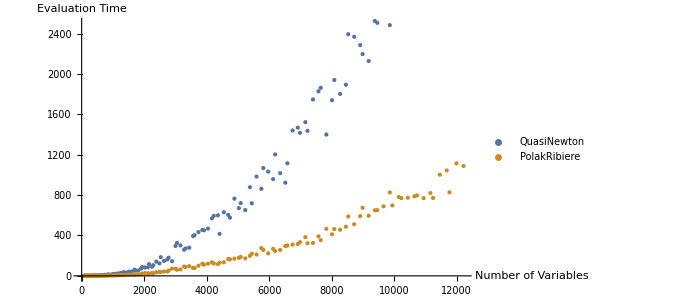

```mathematica
ListPlot[
{Legended[Table[{entry["VariableCount"],entry["QuasiNewton"]["EvaluationTime"]},{entry,Last/@res}],"QuasiNewton"],Legended[Table[{entry["VariableCount"],entry["PolakRibiere"]["EvaluationTime"]},{entry,Last/@res}],"PolakRibiere"]},AxesLabel->{"Number of Variables","Evaluation Time"}]
```

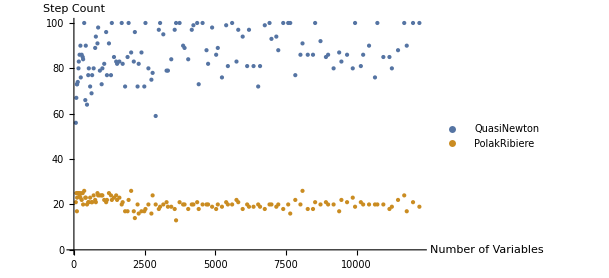

```mathematica
ListPlot[
{Legended[Table[{entry["VariableCount"],entry["QuasiNewton"]["StepCount"]},{entry,Last/@res}],"QuasiNewton"],Legended[Table[{entry["VariableCount"],entry["PolakRibiere"]["StepCount"]},{entry,Last/@res}],"PolakRibiere"]},AxesLabel->{"Number of Variables","Step Count"}]
```

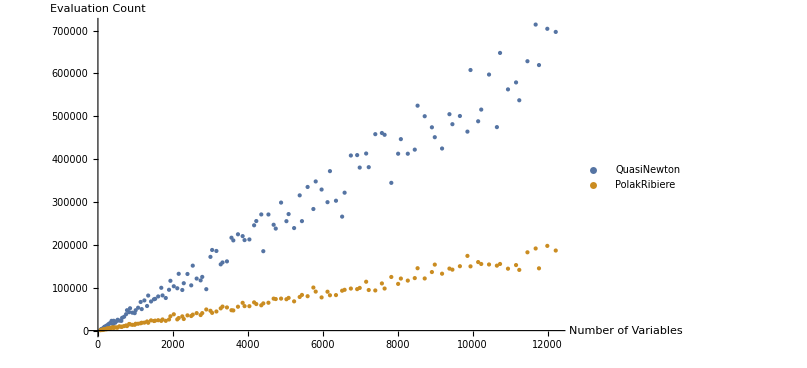

```mathematica
ListPlot[
{Legended[Table[{entry["VariableCount"],entry["QuasiNewton"]["EvaluationCount"]},{entry,Last/@res}],"QuasiNewton"],Legended[Table[{entry["VariableCount"],entry["PolakRibiere"]["EvaluationCount"]},{entry,Last/@res}],"PolakRibiere"]},AxesLabel->{"Number of Variables","Evaluation Count"}]
```